Modelo Dinámico de un eslabón sometido a un sistema de fuerzas externas

{{q→InterpolatingFunction[…]}}

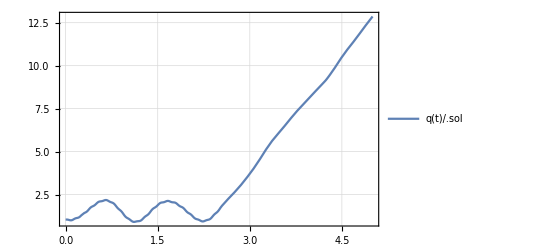

```mathematica
(*datos*)
r2=5;
m[2]=1.5;
Icm[2]=3.136;
g=9.81;
FAx=150 Sin[50 t];
FAy=If[t<2.5,100,0];
tao2=-50 Sin[10 t];
(*coeficientes de velocidad secundarios*)
x[2]=(r2/2) Cos[q];
y[2]=(r2/2) Sin[q];
(*coeficientes de velocidad c-m-*)
ka[2]=1;
kx[2]=Dt[x[2],q];
ky[2]=Dt[y[2],q];
(*Derivadas de los coeficietes de velocidad*)
La[2]=Dt[ka[2],q];
Lx[2]=Dt[kx[2],q];
Ly[2]=Dt[ky[2],q];

(*coeficientes de velocidad del punto de aplicacion de FA*)
xA=r2 Cos[q];
yA=r2 Sin[q];
kAx=Dt[xA,q];
kAy=Dt[yA,q];

Qnc=tao2 ka[2]+FAx kAx + FAy kAy;
Ig=∑_(i=2)^2 (m[i](kx[i]^2+ky[i]^2)+Icm[i] ka[i]^2);
dIg=∑_(i=2)^2 (m[i](kx[i] Lx[i]+ky[i] Ly[i])+Icm[i] ka[i] La[i]);
dvdq=∑_(i=2)^2 m[i] g ky[i];
f=Qnc==Ig qpp + dIg qp^2 + dvdq;
F=f/.{q->q[t],qp->q'[t],qpp->q''[t]};
sol=NDSolve[{F,q[0]==Pi/3,q'[0]==0},q,{t,0,5}]
Plot[q[t]/.sol,{t,0,5},PlotTheme->"Detailed",PlotRange->All]
```